## Running

To run these tests, select the menu Evaluation -> Evaluate notebook.

Clicking “Run” in the “Testing Notebook” toolbar does not work, as it does not run the initialisation section.

## Initialise

### Load packages

```mathematica
<<EccentricIMR`
```

### Define functions

```mathematica
tPeak=0.50003;
```

```mathematica
gaussian=Table[{t,Exp[-(t-tPeak)^2]},{t,0,1,0.1}];
```

```mathematica
cos=N@Table[{t,Cos[t]},{t,0,2Pi,2Pi/10}];
```

```mathematica
sin=N@Table[{t,Sin[t]},{t,0,2Pi,2Pi/10}];
```

```mathematica
hData=Table[{t,t^2 Exp[I 4Pi t^2]},{t,0,1,0.1}];
```

```mathematica
hData2=Table[{t,t Exp[I 6Pi t^3]},{t,0,1,0.05}];
```

## Run tests

### timeToMergerFunction

EccentricIMR`EccentricIMR`Private`timeToMergerFunction[][q,e,l]

391.196+3.13391 e-2492.95 e^2+2.77212 q-17.92 e q+8.11842 q^2+76.4944 e Cos[63.4585-l]+1.15497 q Cos[1.02275+l]

|  | "" |  | "»"

|  | "" | "" |

### timeOfPeak

tPeakFound=EccentricIMR`EccentricIMR`Private`timeOfPeak[gaussian]

0.50003

|  | "" |  | "»"

|  | "" | "" |

```mathematica
tPeak-tPeakFound
```

3.37648×10^-8

### shifted

cosShifted=EccentricIMR`EccentricIMR`Private`shifted[cos,0.3]

{{0.3,1.},{0.928319,0.809017},{1.55664,0.309017},{2.18496,-0.309017},{2.81327,-0.809017},{3.44159,-1.},{4.06991,-0.809017},{4.69823,-0.309017},{5.32655,0.309017},{5.95487,0.809017},{6.58319,1.}}

|  | "" |  | "»"

|  | "" | "" |

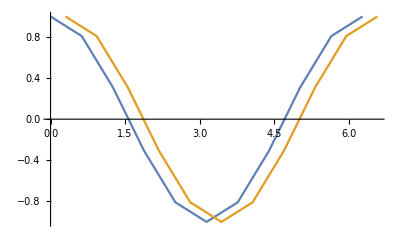

```mathematica
ListLinePlot[{cos,cosShifted}]
```

cosShifted[[1]]

{0.3,1.}

|  | "" |  | "»"

|  | "" | "" |

```mathematica
cos[[1]]
```

{0.,1.}

### phase

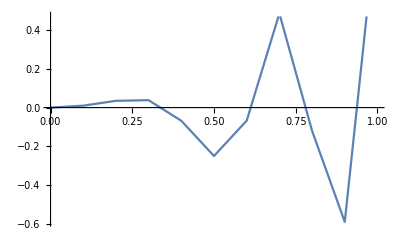

```mathematica
ListLinePlot[Re[hData]]
```

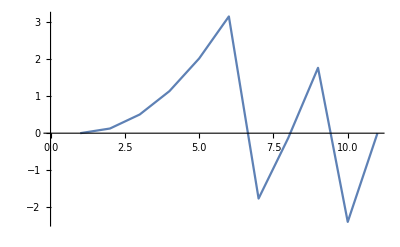

```mathematica
ListLinePlot[Arg[hData[[All,2]]]]
```

phaseData=EccentricIMR`EccentricIMR`Private`phase[hData]

{{0.,0.},{0.1,0.125664},{0.2,0.502655},{0.3,1.13097},{0.4,2.01062},{0.5,3.14159},{0.6,4.52389},{0.7,6.15752},{0.8,8.04248},{0.9,10.1788},{1.,12.5664}}

|  | "" |  | "»"

|  | "" | "" |

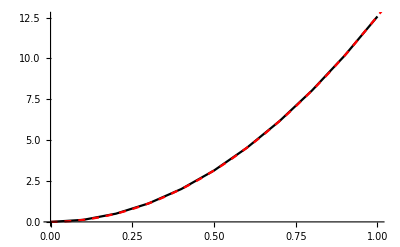

```mathematica
Show[ListLinePlot[phaseData,PlotStyle->Black],Plot[4Pi t^2,{t,0,10},PlotStyle->Directive[Red,Dashed]]]
```

### nderivative

dcos=EccentricIMR`EccentricIMR`Private`nderivative[1][cos,DifferenceOrder→8]

{{0.,0.00182121},{0.628319,-0.588003},{1.25664,-0.950998},{1.88496,-0.951084},{2.51327,-0.587765},{3.14159,4.996×10^-16},{3.76991,0.587765},{4.39823,0.951084},{5.02655,0.950998},{5.65487,0.588003},{6.28319,-0.00182121}}

|  | "" |  | "»"

|  | "" | "" |

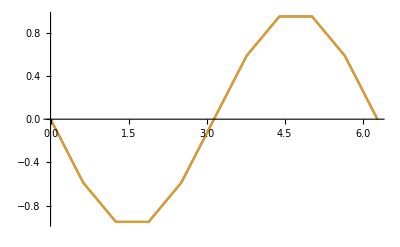

```mathematica
ListLinePlot[{dcos,MapAt[Minus,sin,{All,2}]}]
```

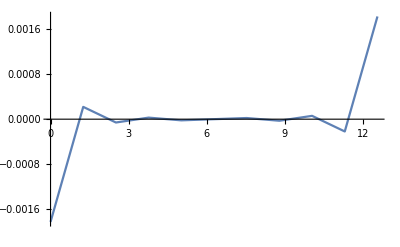

```mathematica
ListLinePlot[MapAt[Minus,dcos+sin,{All,2}],PlotRange->All]
```

### frequency

testFreq=EccentricIMR`EccentricIMR`Private`frequency[hData]

{{0.,-1.77636×10^-15},{0.1,2.51327},{0.2,5.02655},{0.3,7.53982},{0.4,10.0531},{0.5,12.5664},{0.6,15.0796},{0.7,17.5929},{0.8,20.1062},{0.9,22.6195},{1.,25.1327}}

|  | "" |  | "»"

|  | "" | "" |

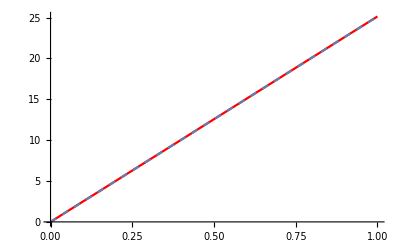

```mathematica
Show[ListLinePlot[testFreq,PlotStyle->Red],Plot[8Pi t,{t,0,1},PlotStyle->Dashed]]
```

### resampled

```mathematica
resTimes=Range[0,2Pi,0.3]
```

{0.,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.}

testRes=EccentricIMR`EccentricIMR`Private`resampled[cos,resTimes]

{{0.,1.},{0.3,0.955452},{0.6,0.825342},{0.9,0.621588},{1.2,0.362354},{1.5,0.070745},{1.8,-0.2272},{2.1,-0.50485},{2.4,-0.737396},{2.7,-0.904072},{3.,-0.989993},{3.3,-0.987477},{3.6,-0.896755},{3.9,-0.725935},{4.2,-0.490265},{4.5,-0.210793},{4.8,0.0875067},{5.1,0.377973},{5.4,0.63467},{5.7,0.834724},{6.,0.960291}}

|  | "" |  | "»"

|  | "" | "" |

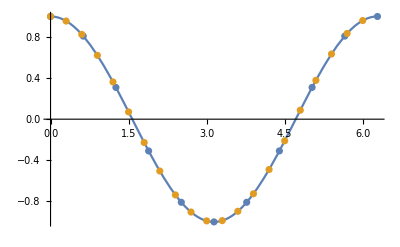

```mathematica
Show[Plot[Cos[t],{t,0,2Pi}],ListPlot[{cos,testRes}]]
```

### planckTaperFunction

```mathematica
tapTimes=Range[-3,3,0.1];
```

testTapFun=EccentricIMR`EccentricIMR`Private`planckTaperFunction[tapTimes,{-1.5,1.5}]

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,8.93095×10^-7,0.000137894,0.00175041,0.00816257,0.0229774,0.0482748,0.0842185,0.12957,0.182426,0.240795,0.302941,0.367493,0.433433,0.5,0.566567,0.632507,0.697059,0.759205,0.817574,0.87043,0.915782,0.951725,0.977023,0.991837,0.99825,0.999862,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

|  | "" |  | "»"

|  | "" | "" |

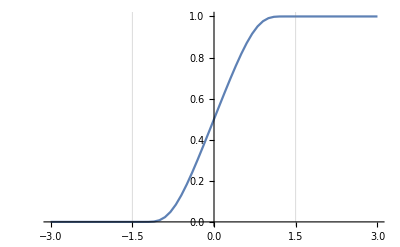

```mathematica
ListLinePlot[Transpose[{tapTimes,testTapFun}],GridLines->{{-1.5,1.5},None}]
```

### planckTaperData

```mathematica
tapDataTimes={{2Pi/8,4Pi/8},{12Pi/8,14Pi/8}}
```

{{π/4,π/2},{(3 π)/2,(7 π)/4}}

testTapData=EccentricIMR`EccentricIMR`Private`planckTaperData[cos,tapDataTimes]

{{0.,0.},{0.628319,0.},{1.25664,0.215403},{1.88496,-0.309017},{2.51327,-0.809017},{3.14159,-1.},{3.76991,-0.809017},{4.39823,-0.309017},{5.02655,0.215403},{5.65487,0.},{6.28319,0.}}

|  | "" |  | "»"

|  | "" | "" |

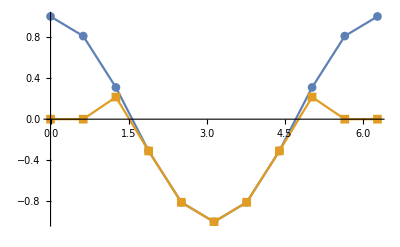

```mathematica
ListLinePlot[{cos,testTapData},GridLines->{Flatten[tapDataTimes],None},PlotMarkers->Automatic]
```

### blend

```mathematica
blendt=Pi/2;
```

```mathematica
blendtau=3Pi/4;
```

testBlend=EccentricIMR`EccentricIMR`Private`blend[cos,sin,blendtau,blendt]

{{0.,1.},{0.628319,0.809017},{1.25664,0.309017},{1.88496,-0.306811},{2.51327,-0.385869},{3.14159,-0.182426},{3.76991,-0.587785},{4.39823,-0.951057},{5.02655,-0.951057},{5.65487,-0.587785},{6.28319,0.}}

|  | "" |  | "»"

|  | "" | "" |

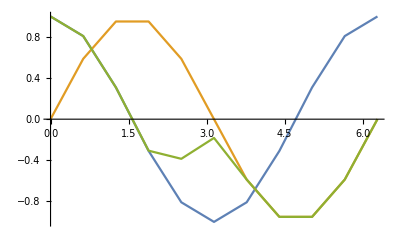

```mathematica
ListLinePlot[{cos,sin,testBlend},GridLines->{{blendt,blendt+blendtau},None}]
```

### blendWaveforms

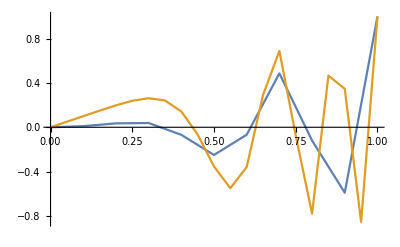

```mathematica
ListLinePlot[Re/@{hData,hData2}]
```

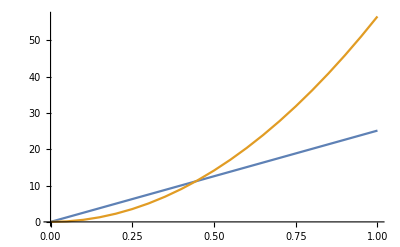

```mathematica
ListLinePlot[EccentricIMR`EccentricIMR`Private`frequency/@{hData,hData2},PlotRange->All]
```

```mathematica
blendhsts={0.4,0.8};
```

testBlendhs=EccentricIMR`EccentricIMR`Private`blendWaveforms[{hData,hData2},blendhsts]

{{0.,0.+0. ⅈ},{0.1,0.00991998+0.00126251 ⅈ},{0.2,0.0350344+0.0193026 ⅈ},{0.3,0.0382485+0.0814681 ⅈ},{0.45,-0.16965+0.115236 ⅈ},{0.5,-0.266241-0.0007593 ⅈ},{0.55,-0.281382-0.227061 ⅈ},{0.6,-0.0433745-0.478036 ⅈ},{0.65,0.459427-0.367172 ⅈ},{0.7,0.585597+0.357996 ⅈ},{0.75,-0.331984+0.679061 ⅈ},{0.8,-0.665641-0.44376 ⅈ},{0.85,0.684815-0.50015 ⅈ},{0.9,0.0344965+0.899339 ⅈ},{0.95,-0.654487-0.691326 ⅈ},{1.,0.935097+0.354392 ⅈ}}

|  | "" |  | "»"

|  | "" | "" |

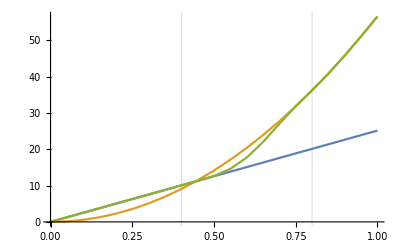

```mathematica
ListLinePlot[EccentricIMR`EccentricIMR`Private`frequency/@{hData,hData2,testBlendhs},PlotRange->All,GridLines->{blendhsts,None}]
```

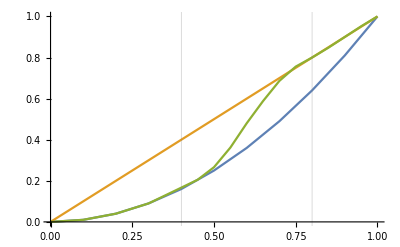

```mathematica
ListLinePlot[Abs/@{hData,hData2,testBlendhs},PlotRange->All,GridLines->{blendhsts,None}]
```

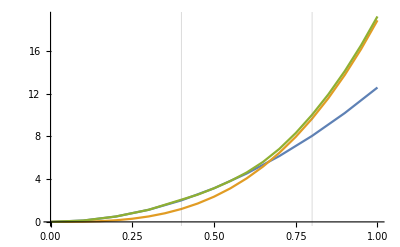

```mathematica
ListLinePlot[EccentricIMR`EccentricIMR`Private`phase/@{hData,hData2,testBlendhs},PlotRange->All,GridLines->{blendhsts,None}]
```

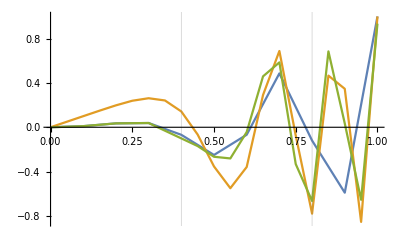

```mathematica
ListLinePlot[Re/@{hData,hData2,testBlendhs},PlotRange->All,GridLines->{blendhsts,None}]
```

### EccentricIMRWaveform

```mathematica
params=<|"q"->1,"x0"->0.1,"e0"->0.1,"l0"->0,"phi0"->0,"t0"->0|>;
```

testhIMR=EccentricIMRWaveform[params,N@{0,1000000}];
testhIMR[[1;;-1;;50]]

{{0.,-0.182628+0.00135133 ⅈ},{50.,0.127144-0.106564 ⅈ},{100.,-0.103199+0.0999756 ⅈ},{150.,0.123069-0.0676607 ⅈ},{200.,-0.1435+0.0696137 ⅈ},{250.,0.0677539-0.18116 ⅈ},{300.,0.18471+0.0766522 ⅈ},{331.289,-0.14034-0.123097 ⅈ},{351.289,-0.103811+0.145727 ⅈ},{371.289,0.146558+0.0963808 ⅈ},{391.289,0.0913812-0.153146 ⅈ},{411.289,-0.172007-0.0737586 ⅈ},{431.289,-0.0234752+0.198069 ⅈ},{451.289,0.198972-0.0748927 ⅈ},{471.289,-0.193496-0.114369 ⅈ},{491.289,0.0790187+0.223167 ⅈ},{511.289,0.0313145-0.250874 ⅈ},{531.289,-0.0661871+0.269483 ⅈ},{551.289,-0.0799215-0.308768 ⅈ},{571.289,0.325825-0.208483 ⅈ},{591.289,-0.21407-0.0785341 ⅈ},{611.289,0.0217441-0.0395532 ⅈ},{631.289,0.00741558+0.0034935 ⅈ},{651.289,-0.000552877+0.00137834 ⅈ}}

|  | "" |  | "»"

|  | "" | "" |

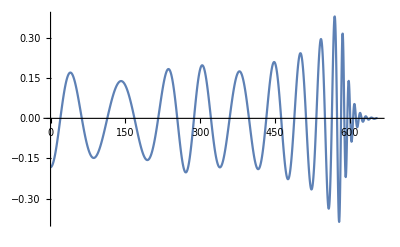

```mathematica
ListLinePlot[Re[testhIMR]]
```

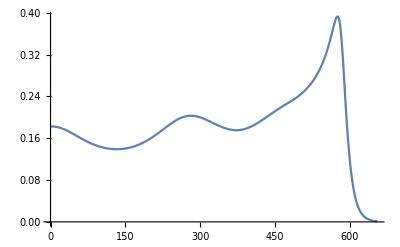

```mathematica
ListLinePlot[MapAt[Abs,testhIMR,{All,2}]]
```